# Distribution of G_6(r)

## The Sum of a Normal Distribution Squared.

```mathematica
DateString[]
```

Thu 2 Jul 2026 11:06:00

First, the distribution of the square.

```mathematica
p=TransformedDistribution[x^2, x\[Distributed]NormalDistribution[0,σ]]
```

TransformedDistribution[x^2,x\[Distributed]NormalDistribution[0,σ]]

Mathematica does not recognize this as an existing distribution.

```mathematica
pdf[s_, x_]:=PDF[p,x]//. σ-> s;
pdf[w,x]
```

Piecewise[{{(ⅇ^(-x/(2 w^2)))/(√(2 π) w √x), x>0}, {0, x<0}, {Indeterminate, True}}]

It can, however, report the mean and variance.

```mathematica
{Mean[p],Variance[p]}
```

{σ^2,2 σ^4}

It can also plot it if we give it a real standard deviation.

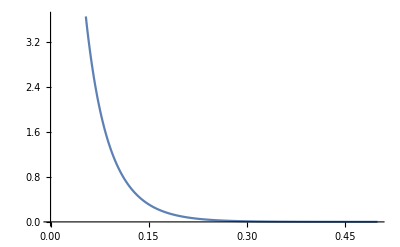

```mathematica
Plot[Evaluate[pdf[π/20,x]],{x,0,.5}]
```

No way to simplify it though.

```mathematica
FullSimplify[p, Assumptions->σ>0]
```

TransformedDistribution[x^2,x\[Distributed]NormalDistribution[0,σ]]

This looks like a Gamma Distribution with (using the Wikipedia definition) α = 1/2, and θ = 2σ^2.

```mathematica
PDF[GammaDistribution[α, θ],x]
```

Piecewise[{{(ⅇ^(-x/θ) x^(-1+α) θ^-α)/Gamma[α], x>0}, {0, True}}]

While that looks pretty well behaved, Gamma(x) = (x-1)!, so

```mathematica
g=FullSimplify[PDF[GammaDistribution[1/2, 2σ^2],x]]
```

Piecewise[{{(ⅇ^(-x/(2 σ^2)))/(√(2 π) √(x σ^2)), x>0}, {0, True}}]

The expression below proves that the square of a Normal is a Gamma Distribution

```mathematica
FullSimplify[g==pdf[σ,x],Assumptions->{σ>0, x>0}]
```

True

Here is an example of a sum of squares of a normal distribution with a small variance.

```mathematica
RandomVariate[NormalDistribution[0,π/20],10]
```

{-0.0431747,-0.115465,-0.00312521,0.0186598,-0.0856394,-0.0109663,0.135176,-0.0660068,0.454969,-0.178125}

We can square each point thus:

```mathematica
Map[#^2&,%]
```

{0.00186405,0.0133321,9.76695×10^-6,0.00034819,0.00733411,0.00012026,0.0182725,0.00435689,0.206997,0.0317284}

And the sum is performed thus:

```mathematica
Apply[ Plus, %]
```

0.284363

This function will create a list of random normal samples, square them, and add them.

```mathematica
sg[n_]:=Apply[ Plus,Map[ #^2&,RandomVariate[NormalDistribution[0,π/20],n]]];
```

Here are five samples of a sum of fifty:

```mathematica
Table[sg[50],5]
```

{1.16448,1.30128,1.19254,0.961459,1.53659}

And here is their mean and variance.

```mathematica
fivesg50mv={Mean[%], Variance[%]}
```

{1.23127,0.0442202}

A sum of 50 should still be Gamma and have an α of 50/2 = 25, and  same θ = 2σ^2 = 2π^2/400.

```mathematica
α1=50/2; θ1=2(π/20)^2;
```

```mathematica
N[{α1,θ1}]
```

{25.,0.049348}

```mathematica
g50=GammaDistribution[α1,θ1]
```

GammaDistribution[25,π^2/200]

This is not trivial to compute with.

```mathematica
PDF[g50,x]
```

Piecewise[{{(1280000000000000000000000000000000000000000000000 ⅇ^(-(200 x)/π^2) x^24)/(236682282155319 π^50), x>0}, {0, True}}]

```mathematica
gn50=N[PDF[g50,x]]
```

Piecewise[{{7.50846×10^8 2.71828^(-20.2642 x) x^24, x>0.}, {0., True}}]

The mean and variance is what we expect:

```mathematica
{Mean[g50], Variance[g50]}
```

{π^2/8,π^4/1600}

```mathematica
N[%]
```

{1.2337,0.0608807}

Let' s compare this to the norm mean and variance:

```mathematica
{α1 θ1,α1 θ1^2}
```

{π^2/8,π^4/1600}

```mathematica
N[%]
```

{1.2337,0.0608807}

The standard deviation is

```mathematica
Sqrt[α1]θ1
```

π^2/40

```mathematica
N[%]
```

0.24674

Finally, let’s compare it to the mean and variance of a mere five samples:

```mathematica
N[% - fivesg50mv]
```

{-0.984532,0.20252}

Here is a plot of that distribution

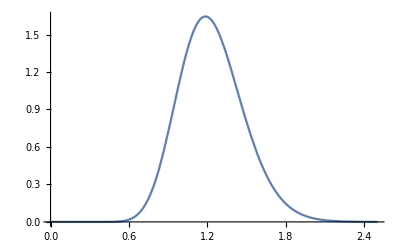

```mathematica
pgn50=Plot[gn50, {x,0,2.5}]
```

The plot below overlays that PDF with a histogram created by 1,000 samples of summing fifty Γ[1/2, π/20] random variables.

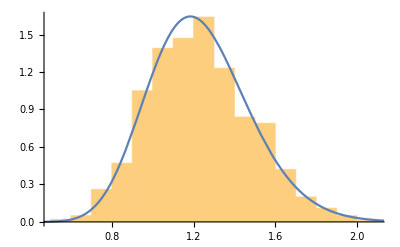

```mathematica
pgn50h=Show[Histogram[Table[sg[50], 1000],Automatic,"PDF"],pgn50]
```

Below we overlay the Normal distribution (in red) with the same mean and variance.

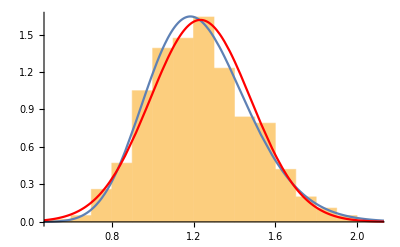

```mathematica
Show[pgn50h,Plot[ Evaluate[PDF[NormalDistribution[α1 θ1,Sqrt[α1]θ1],x]],{x,0,2.5},PlotStyle->Red]]
```

## The Order Parameter

Here is an example of a single set of six evenly spaced particles at a significant rotation:

```mathematica
Table[6I(π/10.0+k π/6),{k, 6}]
```

{0.+5.02655 ⅈ,0.+8.16814 ⅈ,0.+11.3097 ⅈ,0.+14.4513 ⅈ,0.+17.5929 ⅈ,0.+20.7345 ⅈ}

We can compute the complex exponent so:

```mathematica
Map[Exp,%]
```

{0.309017-0.951057 ⅈ,-0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,-0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,-0.309017+0.951057 ⅈ}

Its sum is still near zero.

```mathematica
Apply[Plus,%]/6
```

5.55112×10^-17+1.85037×10^-17 ⅈ

Here is a plot of the constellation of 6 points around a center point.

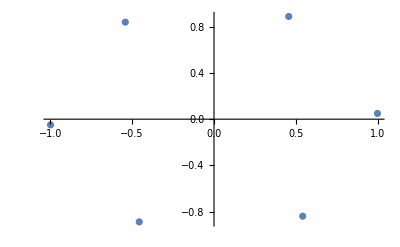

```mathematica
ListPlot[Transpose[{Re[#],Im[#]}]]&[Exp[Table[I(θ1+2π k/6),{k, 0,6-1}]]]
```

This function will create a g_6 with n evenly spaced particles, randomly rotated and adding a bit of noise to each particle’s position, with a normally distributed angles.

```mathematica
ClearAll[g6];
g6::usage="g6[n,a,b] returns a single complex number representing the 6-fold order function 
on a constellation of n particles, with the constellation rotated by a angle θ1 drawn
from a Normal[0,a] distribution, with each particle's position deviated by an angle
ϕ drawn from a Normal[0,b] distribution. a and b both default to π/72.";
g6[n_,a_:π/72,b_:π/72]:=Module[{θ1=RandomVariate[NormalDistribution[0,a]],c,d},(*θ1 is a random rotation *)
				c=Table[(θ1+2π k/n),{k,0,n-1}]+
					   RandomVariate[NormalDistribution[0,b],n];
				d=Apply[Plus,Map[Exp,6I(c)]]/n]
```

For five and seven particles, it is near zero in magnitude. For six particles, it is near one.

```mathematica
{g6[5],g6[6],g6[6],g6[7]}
```

{0.0674609-0.105163 ⅈ,0.909244+0.231125 ⅈ,0.976212-0.0234138 ⅈ,0.00322346-0.0304606 ⅈ}

```mathematica
Abs[%]
```

{0.124941,0.93816,0.976493,0.0306307}

The plot below shows the thin arc due to the static crystal rotation (blue), the cluster caused by noise in the particle positions (green), and the effect of both (orange). The unit circle is in red.

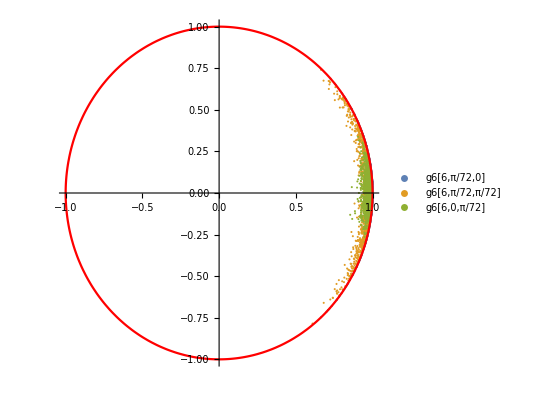

```mathematica
Show[ListPlot[{Table[{Re[#],Im[#]}&[g6[6,π/72,0.0001]],1000],
		Table[{Re[#],Im[#]}&[g6[6,π/72,π/72]],1000],
		Table[{Re[#],Im[#]}&[g6[6,0.0001,π/72]],1000]},
		 AspectRatio->1,AxesOrigin->{0,0},
		 PlotLegends->{"g6[6,π/72,0]","g6[6,π/72,π/72]","g6[6,0,π/72]"}],
ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π},PlotStyle->{Red},
	 AspectRatio->1,AxesOrigin->{0,0}],PlotRange->All]
```

Here is a histogram of the magnitude of the six particle version.

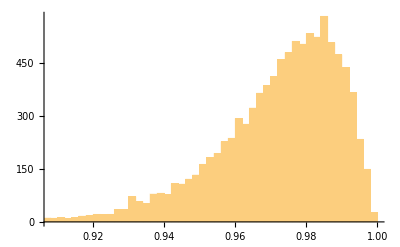

```mathematica
g66t=Table[Abs[g6[6]],10000];
Histogram[g66t,50]
```

```mathematica
{Mean[#],Variance[#]}&[g66t]
```

{0.97182,0.000310868}

That small variance is due to the random angle.

The plot below shows the same for the n = 7 version.  The g6[7,π/72,0] cluster is very close to the origin as rotating the constellation of 7 evenly spaced particles still sums to zero.

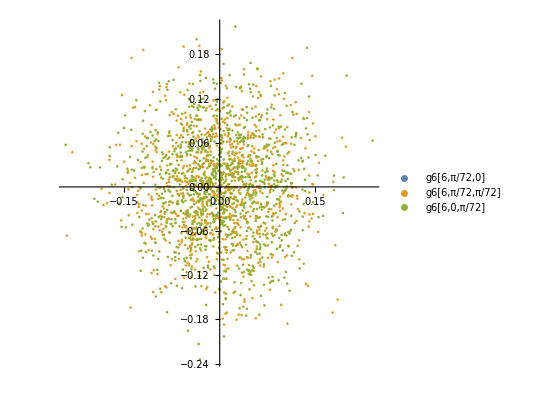

```mathematica
ListPlot[{Table[{Re[#],Im[#]}&[g6[7,π/72,0.0001]],1000],
		Table[{Re[#],Im[#]}&[g6[7,π/72,π/72]],1000],
		Table[{Re[#],Im[#]}&[g6[7,0.0001,π/72]],1000]},
		 AspectRatio->1,AxesOrigin->{0,0},
		 PlotLegends->{"g6[6,π/72,0]","g6[6,π/72,π/72]","g6[6,0,π/72]"}]
```

Here is the seven particle version of the histogram.  The five particle looked similar (re-evaluate the cell below with g6[5] instead of g6[7]), and they both look like Rayleigh distributions.

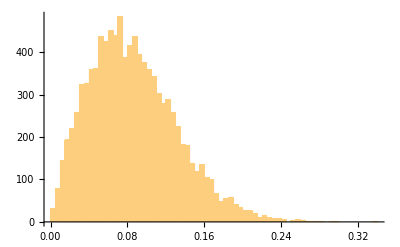

```mathematica
g67t=Table[Abs[g6[7]],10000];
Histogram[g67t,50]
```

```mathematica
{Mean[#],Variance[#]}&[g67t]
```

{0.0859883,0.00203823}

Wikipidia’s article on Circular uniform distribution indicates that the mean of samples from a circle will be Rayleigh distributed with scale parameter σ = √(1/2N). In the above, g6[7] would be with N = 7. The variance of a Rayleigh distribution is ((4-π)/2)σ^2, and the mean is σ√(π/2)

```mathematica
N[{(√(1/(2 7)))√(π/2),(1/(2 7))(4-π)/4}]
```

{0.334962,0.0153287}

#### Symbolic Analysis of g_6

It concerned me that the five and seven summed so close to zero. Here is a symbolic analysis.

```mathematica
Sum[Exp[6I (2j π/7)],{j,0,6}]
```

1+ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7)+ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7)+ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7)

It will simplify:

```mathematica
FullSimplify[%]
```

0

This is fundamental to the DFT, where ∑_(i=0)^(N-1) e^(j2πi(m-n)/N)=0 unless n = m (j is the imaginary unit). It is so as the finite geometric sum ∑_(i=0)^(N-1) r^i =(1-r^N)/(1-r)for r≠1.  Here r=e^(j2π(m-n)/N), so when m, n, and N are integers, r^N=e^(j2π(m-n))=1, so the numerator is zero, the denominator is a complex number, but the quotient is zero.

Order Parameter Products

The estimate of the expected value of sum of products looks like the following.

```mathematica
g6[6]Conjugate[g6[6]]
```

0.975125-0.0552652 ⅈ

```mathematica
Abs[%]
```

0.976689

Here is a histogram of 10,000 such products for six particles.

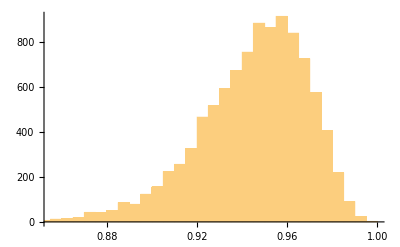

```mathematica
g6pt=Table[ Abs[g6[6]Conjugate[g6[6]]], 10000];
Histogram[ g6pt,50]
```

So that looks pretty very much like the simple g6 histogram.  The variance is a bit bigger that the single sample g6.

```mathematica
mvg6pt={Mean[#],Variance[#]}&[g6pt]
```

{0.944689,0.000581823}

The product of a g6[6] and g6[5] looks Rayleigh:

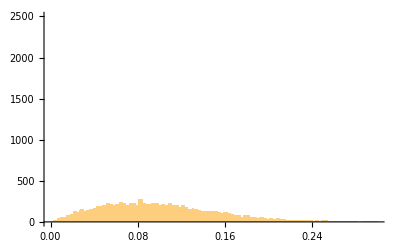

```mathematica
g6p5t=Table[ Abs[g6[6]Conjugate[g6[5]]], 10000];
Histogram[ g6p5t,{0,0.3,0.3/100},PlotRange->{{0,0.3},{0,2500}}]
```

```mathematica
mvg6p5t={Mean[#],Variance[#]}&[g6p5t]
```

{0.0990382,0.00270179}

```mathematica
s2=mvg6p5t⟦2⟧(10000-1)/20000
```

0.00135076

A true Rayleigh distribution will have this relation for the mean and variance μ^2/σ^2:

```mathematica
1.253^2/.429
```

3.65969

```mathematica
Simplify[(σ^2 π/2)/(σ^2(2-π/2))]
```

π/(4-π)

```mathematica
N[%]
```

3.65979

Which is reasonably close to what is observed.

```mathematica
mvg6p5t⟦1⟧^2/mvg6p5t⟦2⟧
```

3.6304

So, the variance of the 5 & 6 particle correlation is larger than the 6 & 6.

```mathematica
Sqrt[mvg6pt⟦2⟧/mvg6p5t⟦2⟧]
```

0.464055

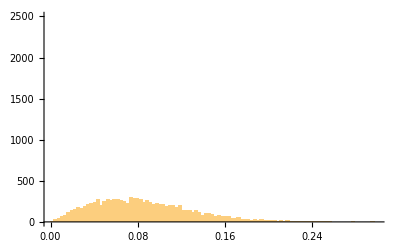

```mathematica
g6p7t=Table[ Abs[g6[6]Conjugate[g6[7]]], 10000];
Histogram[ g6p7t,{0,0.3,0.3/100},PlotRange->{{0,0.3},{0,2500}}]
```

```mathematica
mvg6p7t={Mean[#],Variance[#]}&[g6p7t]
```

{0.0839309,0.00196017}

```mathematica
mvg6p7t⟦1⟧^2/mvg6p7t⟦2⟧
```

3.59377

The g6g6* variance is about two times bigger.

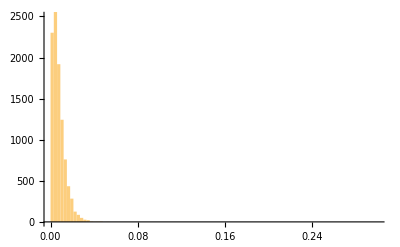

```mathematica
g5p5t=Table[ Abs[g6[7]Conjugate[g6[7]]], 10000];
Histogram[ g5p5t,{0,0.3,0.3/100},PlotRange->{{0,0.3},{0,2500}}]
```

```mathematica
mvg5p5t={Mean[#],Variance[#]}&[g5p5t]
```

{0.00744594,0.0000344362}

```mathematica
mvg5p5t⟦1⟧^2/mvg5p5t⟦2⟧
```

1.60999

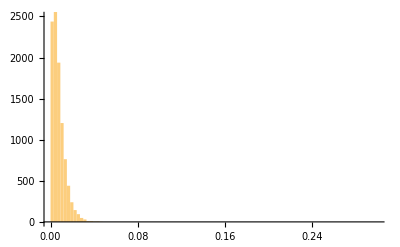

```mathematica
g7p7t=Table[ Abs[g6[7]Conjugate[g6[7]]], 10000];
Histogram[ g7p7t,{0,0.3,0.3/100},PlotRange->{{0,0.3},{0,2500}}]
```

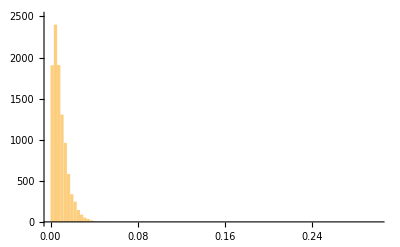

```mathematica
g5p7t=Table[ Abs[g6[5]Conjugate[g6[7]]], 10000];
Histogram[ g5p7t,{0,0.3,0.3/100},PlotRange->{{0,0.3},{0,2500}}]
```

We’ll make a compiled version of g6[n] because the histogram below was very slow to compute.

```mathematica
g6c=Compile[{{n,_Integer},{a,_Real},{b,_Real}},
	Module[{θ1=RandomVariate[NormalDistribution[0,a]],c,d},(*θ1 is a random rotation *)
		   c=Table[(θ1+2π k/n),{k,0,n-1}]+
			 RandomVariate[NormalDistribution[0,b],n];
		   d=Total[Map[Exp,6I(c)]]/n],
			CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
g6[6,π/72,π/72]
```

0.899222+0.410141 ⅈ

```mathematica
g6c[7,π/72,π/72]
```

0.0696926+0.0141852 ⅈ

```mathematica
ClearAll[pairs];
pairs[n_Integer]:=n(n-1)/2
```

```mathematica
pairs[256]
```

32640

The function below will generate a sample of correlation function g6g6* for p percentage of six particle groups, and (1-p) percentage of six and five particle groups and six and seven for n total samples:

```mathematica
ClearAll[mgn6,mgn6c];
mgn6[p_,n_Integer,a_:π/72,b_:π/72]:=
	Module[{n6t=RandomVariate[BinomialDistribution[n,p]],n5,n6,n7,n55,n56,n57,n66,n67,n77,nt},
			n6=If[n6t==0,0,If[OddQ[n6t],n6t+1,n6t]]; (* ensure n6 even *)
			n5=Round[(n-n6)/2]; (* 5 particle samples *)
			n7=n-n6-n5; (* 7 particle samples *)
			n55=pairs[n5]; n56=n6*n5; n66=pairs[n6]; n57=n5*n7; n67=n6*n7; n77=pairs[n7];
			(* Print["n5=",n5,", n6= ",n6,", n7=",n7,{n55,n56,n57,n66,n67,n77}];*)
			nt=Total[{n55,n56,n57,n66,n67,n77}];(* Print[nt]; *)
			<|"g6"->Abs[ (* Take absolute value of the Total *)
				Total[ (* Sum all results together to get a single complex number *)
					Join[Total[Table[g6c[5,a,b]Conjugate[g6c[5,a,b]],n55]],
						 Total[Table[g6c[5,a,b]Conjugate[g6c[6,a,b]],n56]],
						 Total[Table[g6c[5,a,b]Conjugate[g6c[7,a,b]],n57]],
						 Total[Table[g6c[6,a,b]Conjugate[g6c[6,a,b]],n66]],
						 Total[Table[g6c[6,a,b]Conjugate[g6c[7,a,b]],n67]],
						 Total[Table[g6c[7,a,b]Conjugate[g6c[7,a,b]],n77]]]]/nt],
			  "nt"->nt,"n5"->n5,"n6"->n6,"n7"->n7,"pt"->pairs[n]|>]
```

```mathematica
{mgn6[.9,256,N[π/72],N[π/72]],mgn6[.1,1024]}
```

{<|g6→0.749096,nt→32640,n5→14,n6→228,n7→14,pt→32640|>,<|g6→0.00853993,nt→523776,n5→461,n6→102,n7→461,pt→523776|>}

The function below will create a table of K samples of the above function.

```mathematica
ClearAll[tmgn6];
tmgn6[K_Integer,p_,n_Integer,a_:π/72,b_:π/72]:=
	Dataset[ParallelTable[mgn6[p,n,a,b],K]]
```

```mathematica
(tt=tmgn6[5,0.9,256])//AbsoluteTiming
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Sun 1 Oct 2023. Please

{2.21651,Dataset[<>]}

```mathematica
tt[All,"g6"]
```

Dataset[<>]

Here is the histogram at a mean of 0.9 for 175 particles.  This is the number of particles expected in the outer ring of the 16x16 standard array we have been working with.

```mathematica
t=AbsoluteTiming[tmgn6t9=tmgn6[1000,.9,175];]
```

{18.6743,Null}

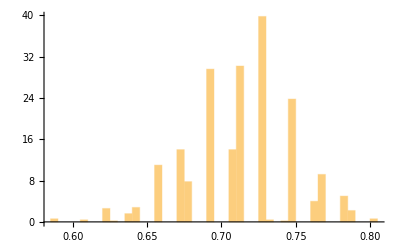

```mathematica
htm9=Histogram[tmgn6t9[All,"g6"],50,"PDF"]
```

```mathematica
tmgn6t9[GroupBy["n5"],Histogram[#,{0.56,0.86,0.2/100}]&,"g6"]
```

Dataset[<>]

```mathematica
tmgn6t9[GroupBy["n5"],{Mean,StandardDeviation, Length},"g6"][SortBy[1]]
```

Dataset[<>]

With the compiled g6c[ ] function, it takes almost 40s to compute the 1,000 samples of 256 particles.

```mathematica
t
```

{18.6743,Null}

```mathematica
tm9={Mean[#],StandardDeviation[#]}&[tmgn6t9[All,"g6"]]
```

{0.712173,0.035635}

```mathematica
tm9⟦2⟧/tm9⟦1⟧
```

0.050037

The standard deviation is 1.6% of the mean. The histogram shows that there are only a few values that show up, not a continuum.

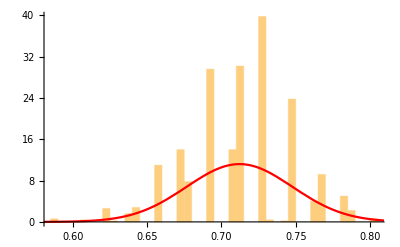

```mathematica
Show[htm9,Plot[ Evaluate[PDF[NormalDistribution[tm9⟦1⟧,tm9⟦2⟧],x]],{x,0.5,0.9},PlotStyle->Red]]
```

If the mean is zero, then we get a more Rayleigh-like distribution, even though it is a sum of 500 samples.

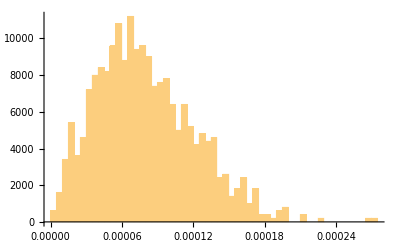

```mathematica
t=AbsoluteTiming[tmgn6tz=tmgn6[1000,0.0,175];];
htm0=Histogram[tmgn6tz[All,"g6"],50,"PDF"]
```

```mathematica
t
```

{19.8018,Null}

The mean is pretty small though.

```mathematica
tm0={Mean[#],StandardDeviation[#]}&[tmgn6tz[All,"g6"]]
```

{0.0000799496,0.0000415984}

```mathematica
tm0⟦2⟧/tm0⟦1⟧
```

0.520307

This shows that the distribution is not normal.

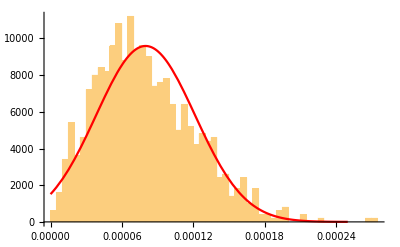

```mathematica
Show[htm0,Plot[ Evaluate[PDF[NormalDistribution[tm0⟦1⟧,tm0⟦2⟧],x]],{x,0.0,0.00025},PlotStyle->Red]]
```

Trajectories

Here are three different trajectories, one constant, one power law, and one exponential. The number of samples we have been working with are 70, with each ring getting a different number of particles.

the swath at r_i=i δr takes in all particles found between (i -1)δr and r_i.

```mathematica
ClearAll[swath];
a[ρ_]:=√(2/(ρ √3)) (* This is the crystal spacing at density ρ *);
swath[r_,δr_,ρ_:1/π]= (* swath width at crystal spacing radius *)
 ρ π FullSimplify[(r a[ρ])^2-(r a[ρ]-δr)^2,Assumptions->{r>0,δr>0,ρ>0}]
```

π (-δr^2+(2 √2 r δr)/(3^(1/4) √ρ)) ρ

```mathematica
N[swath[1,7/100]]
```

0.261748

The solid does not decay, so we will just generate a number of samples that are all the same. We will set the number of samples of G_6 (ns) and the total range, which we will use for all three curves.

```mathematica
ns=70;range=20;
solid = tmgn6[20,0.9,175][All,"g6"]
```

Dataset[<>]

The hexatic phase will decrease algebraically with a worst case of a -1/4 exponent {Halperin1978].

```mathematica
exps=Table[-x,{x,0.05,0.25,0.05}]
```

{-0.05,-0.1,-0.15,-0.2,-0.25}

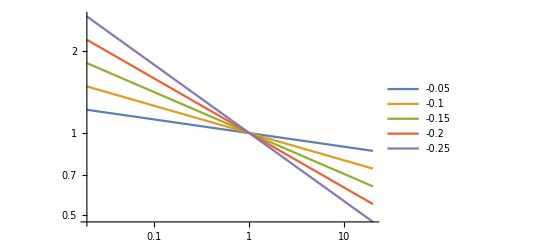

```mathematica
LogLogPlot[{r^-0.05,r^-0.1,r^-0.15,r^-0.2,r^-0.25},{r,0,20},PlotLegends->Table[-x,{x,0.05,0.25,0.05}]]
```

```mathematica
η=-1/4;
semi=Table[mgn6[i^η, 175]["g6"],{i,1,20}]
```

{0.88123,0.606168,0.495558,0.435886,0.381065,0.306551,0.3187,0.319274,0.272267,0.356662,0.250763,0.200177,0.250099,0.20886,0.219676,0.190889,0.271561,0.181726,0.190076,0.209579}

```mathematica
expi = Table[mgn6[Exp[-i/4.0], 175]["g6"],{i,1,20}]
```

{0.541571,0.369378,0.172259,0.107923,0.0597138,0.0317138,0.0313841,0.0129693,0.00515116,0.00517439,0.00518126,0.0024902,0.000869349,0.00259279,0.000316055,0.000606472,0.000153336,0.000339004,0.00032633,0.000191796}

```mathematica
zero=tmgn6[20,0.0,175][All,"g6"]
```

Dataset[<>]

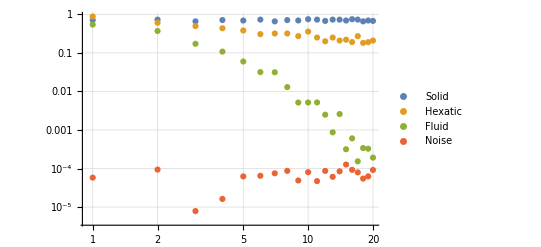

```mathematica
ListLogLogPlot[{solid, semi, expi,zero},GridLines->Automatic,PlotLegends->{"Solid","Hexatic","Fluid","Noise"}]
```

```mathematica
Exp[-4.0]
```

0.0183156

## Deluanay Triangulation

The below is from Appendix D of Salazar-Romero 2017. It is the first step of a DeLuanay triangulation.

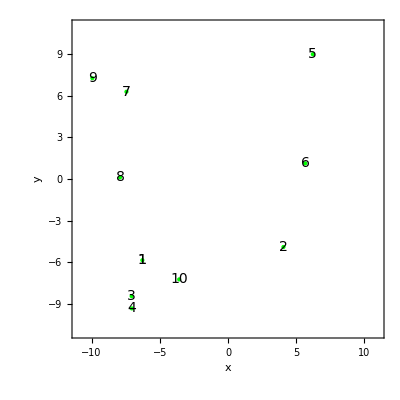

```mathematica
randomPoints=10;initialPoints=RandomReal[{-10,10},{randomPoints,2}];
NPoints=Dimensions[initialPoints]⟦1⟧;
x[i_]:=initialPoints⟦i⟧⟦1⟧; y[i_]:=initialPoints⟦i⟧⟦2⟧;
(* Set up a graphics object to which we can add *)
text=Graphics[Text[Style[ToString[1],14],{x[1],y[1]}]];
labels=text;
For[n=1,n≤NPoints,
text=Graphics[Text[Style[ToString[n],14],{x[n],y[n]}]];
labels=Show[labels,text];
n++];
pointsPlot=ListPlot[initialPoints,Frame->True,PlotStyle->Directive[Green,PointSize[Large]],FrameLabel->{Style["x",14,Black],Style["y",14,Black]},AspectRatio->1,PlotRange->{{-11,11},{-11,11}}];
Show[pointsPlot,labels]
```

```mathematica
circleParameters[index1_,index2_,index3_]:=
(
x1=x[index1]; x2=x[index2]; x3=x[index3];y1=y[index1]; y2=y[index2]; y3=y[index3];
xCenter=(x3^2(y1-y2)+(x1^2+(y1-y2)(y1-y3))(y2-y3)+x2^2(y3-y1))/
(2(x3(y1-y2)+x1(y2-y3)+x2(y3-y1)));
yCenter=(-x2^2 x3+x1^2(x3-x2)+x3(y1-y2)(y1+y2)+x1(x2^2-x3^2+y2^2-y3^2)+x2(x3^2-y1^2+y3^2))/
(2(x3(y1-y2)+x1(y2-y3)+x2(y3-y1)));
R=(1/2)√((((x1-x2)^2+(y1-y2)^2)((x1-x3)^2+(y1-y3)^2)((x2-x3)^2+(y2-y3)^2))/(x3(y2-y1)+x2(y1-y3)+x1(y3-y2))^2);
Return[{xCenter,yCenter,R}])
```

```mathematica
plotCircle[index1_,index2_,index3_]:=(
parameters=circleParameters[index1,index2,index3];
xc=parameters⟦1⟧; yc=parameters⟦2⟧; radius=parameters⟦3⟧;
Return[Graphics[{Gray,Circle[{xc,yc},radius]}]])
```

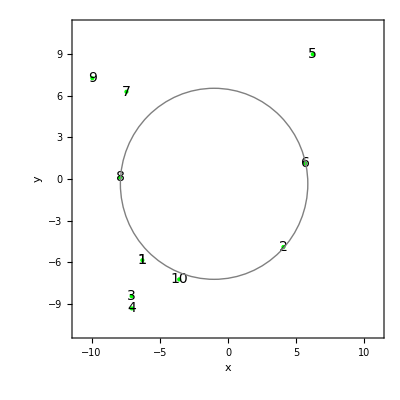

```mathematica
Show[pointsPlot,labels,plotCircle[2,6,8]]
```

```mathematica
(* True if Clockwise *)
clockwise[index1_,index2_,index3_]:=(
x1=x[index1]; x2=x[index2]; x3=x[index3];y1=y[index1]; y2=y[index2]; y3=y[index3];
ux=x2-x1; uy=y2-y1;
vx=x3-x2; vy=y3-y2;
crossProduct=ux vy-uy vx;
crossProduct<0)
```

```mathematica
clockwise[8,6,2]
```

True

```mathematica
inCircle[index1_,index2_,index3_,index4_]:=(
x1=x[index1]; x2=x[index2]; x3=x[index3]; x4=x[index4];y1=y[index1]; y2=y[index2]; y3=y[index3]; y4=y[index4];
testMatrix=({{x4^2+y4^2, x4, y4, 1}, {x1^2+y1^2, x1, y1, 1}, {x2^2+y2^2, x2, y2, 1}, {x3^2+y3^2, x3, y3, 1}});
sign=If[clockwise[index1,index2,index3]==True,1,-1];
testResult=sign Det[testMatrix];
testResult>0
)
```

```mathematica
{inCircle[8,6,2,5],inCircle[8,6,2,7]}
```

{False,False}

## References